```mathematica
(* from RandomAnalyticSignal_Plot *)
(* created at 2011/12/5 *)
```

```mathematica
(* 再実行しても結果が同じになるように *)
SeedRandom[0]
```

```mathematica
numberOfExtremum[li_List]:=Length[Select[Differences[li]*RotateRight[Differences[li]],#≤0&]]
```

```mathematica
(* 線分が交わるかどうかを求める *)
normalize[p_,a_,b_]:=If[b-a≠0,(p-a)/(b-a),ComplexInfinity]
cross0Q::usage="実数区間[x,y]が原点を含むか、ただしx==yのときはFalse";
cross0Q[x_,y_]:=If[x≠y,IntervalMemberQ[Interval[{x,y}],0],False](*(x≥0&&y≤0)||(x≤0&&y≥0)*)
intervalIntersectionQ[a_,b_]:=!((a<0&&b<0)||(a>1&&b>1))
complexToVector[x_]:={Re[x],Im[x]}
cross01Q::usage="入力された2つの複素数で描かれるが線分(0+0ⅈ,1+0ⅈ)と交わるか";
cross01Q[p2_,q2_]:=If[cross0Q[Im[p2],Im[q2]]&&0≤Re[(Im[p2] q2-Im[q2] p2)/(Im[p2]-Im[q2])]≤1,True,If[Im[p2]==0&&Im[q2]==0,intervalIntersectionQ[Im[p2],Im[q2]],False]]
crossQ::usage="線分(p,q)が線分(a,b)と交わるか";
crossQ[{{p_,q_},{a_,b_}}]:=If[a==b,If[p==q,a==p,cross01Q[normalize[a,p,q],normalize[b,p,q]]],cross01Q[normalize[p,a,b],normalize[q,a,b]]]
curveCrossQ[{{p_,q_},{a_,b_}}]:=If[q≠a&&b≠p,crossQ[{{p,q},{a,b}}],False]
```

```mathematica
n=10;
norList1={};
noargeList1={};
noabseList1={};
noreList1={};
lenList1={};
noiList1={};
Do[
(* amp=Table[Random[]/k,{k,1,n}]; *)
amp={1,1,1,1,1,0,0,0,0,0};
rot=Table[2π Random[],{n}];
(* rot={0,0,0,0,0,0,0,0,0,0} *)
c[t_]:=∑_(k=1)^n amp⟦k⟧ Exp[ⅈ k (t-rot⟦k⟧)] ;

(* NumberOfRotation *)
dt=(2π)/100;
argList=Table[Arg[c[t+dt]-c[t]],{t,0,2π,dt}];
nor=Length[Select[Differences[argList],#≤-π&]]-Length[Select[Differences[argList],#≥π&]];(*これが回転数*)
AppendTo[norList1,nor];

(* NumberOfArgExtremum *)
dt=(2π)/200;
argList=Table[Arg[c[t]],{t,0,2π,dt}];
correctionArgList=Rest[argList]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[argList]];
noarge=numberOfExtremum[correctionArgList]/2;
AppendTo[noargeList1,noarge];

(* NumberOfAbsExtremum *)
dt=(2π)/200;
absList=Table[Abs[c[t]],{t,0,2π,dt}];
correctionAbsList=Rest[absList]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[absList]];
noabse=numberOfExtremum[correctionAbsList]/2;
AppendTo[noabseList1,noabse];

(* NumberOfReExtremum *)
dt=(2π)/200;
reList=Table[Re[c[t]],{t,0,2π,dt}];
correctionReList=Rest[reList]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[reList]];
nore=numberOfExtremum[correctionReList]/2;
AppendTo[noreList1,nore];

(* Length *)
dt=(2π)/500;
curveLength=Sum[Abs[c[t+dt]-c[t]],{t,0,2π,dt}];
AppendTo[lenList1,curveLength];

(* NumberOfIntersection *)
dt=(2π)/200;
li=Most[Table[c[t],{t,0,2π,dt}]];
lines={li,RotateLeft[li]}ᵀ;
noi=Count[curveCrossQ/@Subsets[lines,{2}],True];
AppendTo[noiList1,noi];
,{100}]
```

```mathematica
n=10;
norList2={};
noargeList2={};
noabseList2={};
noreList2={};
lenList2={};
noiList2={};
Do[
(* amp=Table[Random[]/k,{k,1,n}]; *)
amp={0,0,0,0,0,1,1,1,1,1};
rot=Table[2π Random[],{n}];
(* rot={0,0,0,0,0,0,0,0,0,0} *)
c[t_]:=∑_(k=1)^n amp⟦k⟧ Exp[ⅈ k (t-rot⟦k⟧)] ;

(* NumberOfRotation *)
dt=(2π)/100;
argList=Table[Arg[c[t+dt]-c[t]],{t,0,2π,dt}];
nor=Length[Select[Differences[argList],#≤-π&]]-Length[Select[Differences[argList],#≥π&]];(*これが回転数*)
AppendTo[norList2,nor];

(* NumberOfArgExtremum *)
dt=(2π)/200;
argList=Table[Arg[c[t]],{t,0,2π,dt}];
correctionArgList=Rest[argList]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[argList]];
noarge=numberOfExtremum[correctionArgList]/2;
AppendTo[noargeList2,noarge];

(* NumberOfAbsExtremum *)
dt=(2π)/200;
absList=Table[Abs[c[t]],{t,0,2π,dt}];
correctionAbsList=Rest[absList]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[absList]];
noabse=numberOfExtremum[correctionAbsList]/2;
AppendTo[noabseList2,noabse];

(* NumberOfReExtremum *)
dt=(2π)/200;
reList=Table[Re[c[t]],{t,0,2π,dt}];
correctionReList=Rest[reList]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[reList]];
nore=numberOfExtremum[correctionReList]/2;
AppendTo[noreList2,nore];

(* Length *)
dt=(2π)/500;
curveLength=Sum[Abs[c[t+dt]-c[t]],{t,0,2π,dt}];
AppendTo[lenList2,curveLength];

(* NumberOfIntersection *)
dt=(2π)/200;
li=Most[Table[c[t],{t,0,2π,dt}]];
lines={li,RotateLeft[li]}ᵀ;
noi=Count[curveCrossQ/@Subsets[lines,{2}],True];
AppendTo[noiList2,noi];

,{100}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
resultPlot[list1_,list2_]:=ErrorListPlot[{{{1,Mean[list1]},ErrorBar[{Min[list1]-Mean[list1],Max[list1]-Mean[list1]}]},{{2,Mean[list2]},ErrorBar[{Min[list2]-Mean[list2],Max[list2]-Mean[list2]}]}},PlotRange->{{0.5,2.5},{0,All}},AspectRatio->2,Ticks->{{{1,"OverTilde[s_1](t)"},{2,"OverTilde[s_2](t)"}}},LabelStyle->(FontSize->20)]
```

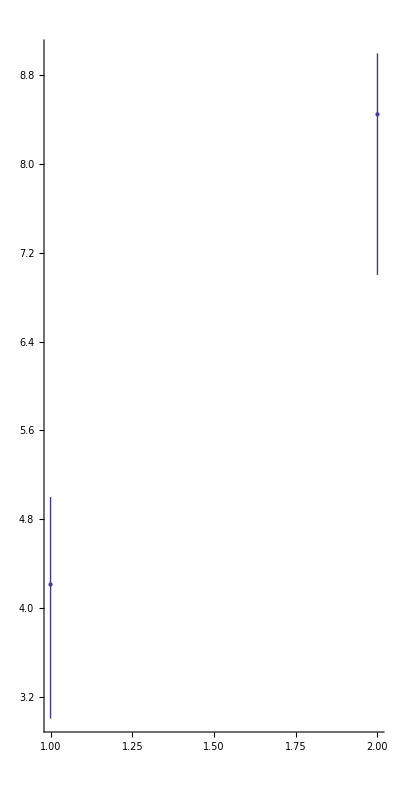

```mathematica
resultPlot[norList1,norList2]
```

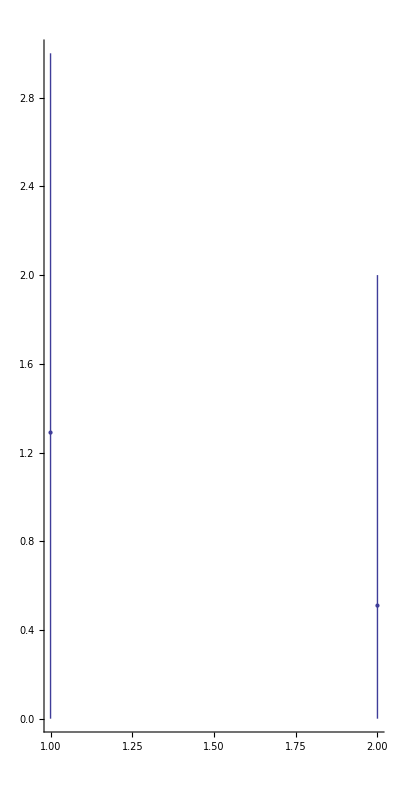

```mathematica
resultPlot[noargeList1,noargeList2]
```

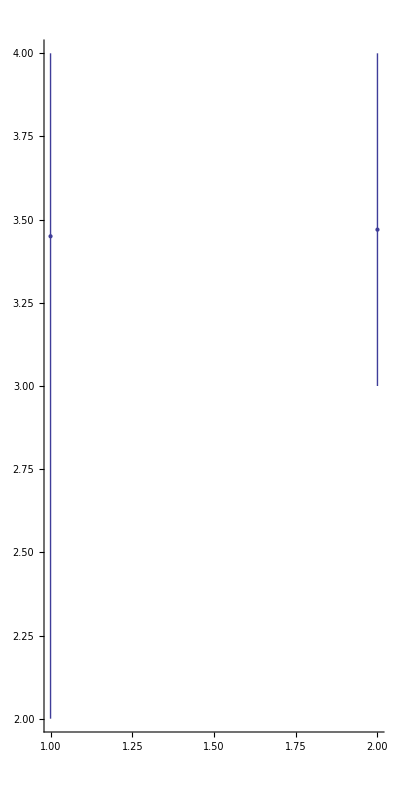

```mathematica
resultPlot[noabseList1,noabseList2]
```

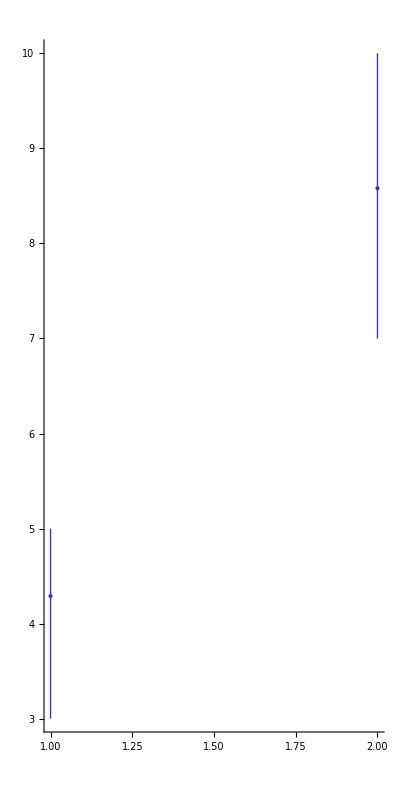

```mathematica
resultPlot[noreList1,noreList2]
```

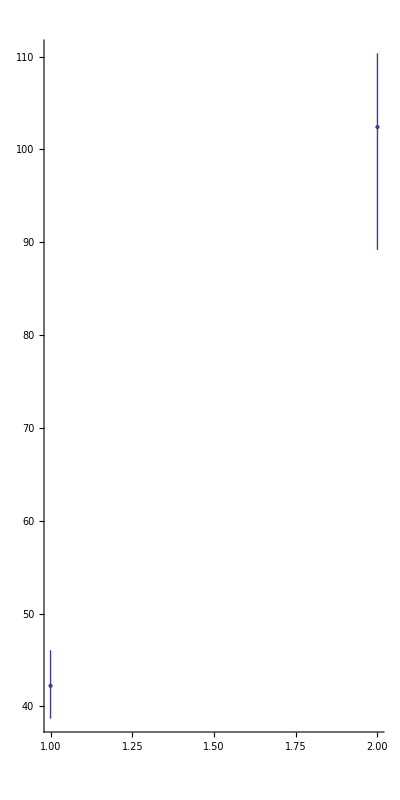

```mathematica
resultPlot[lenList1,lenList2]
```

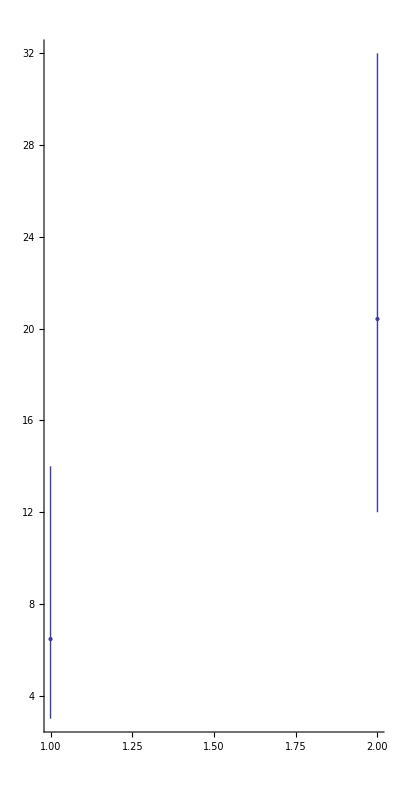

```mathematica
resultPlot[noiList1,noiList2]
```